```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
Δ[r_]:=r^2-2M r+a^2;
Win[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-Δ[r]/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2);
hold=Simplify[Expand[((D[Exp[-ⅈ γ rs] c[k] (r[rs]-rp)^k,{rs,2}]+Win[r[rs]]Exp[-ⅈ γ rs] c[k] (r[rs]-rp)^k)/Exp[-ⅈ γ rs]/.{r[rs]->r,r'[rs]->Δ[r]/r^2,r''[rs]->D[Δ[r]/r^2,r] Δ[r]/r^2})],Assumptions->{ω>0,a>0,m>0,M>0,δ>0}]
```

1/r^6(r-rp)^(-2+k) (a^4 ((2-3 k+k^2) r^2+2 (-2+k) r rp+2 rp^2)-4 a m M r^3 (r-rp)^2 ω-r^2 (-k^2 r^4-4 M^2 ((-1+k)^2 r^2+(-2+k) r rp+rp^2)+k r^4 (1+2 ⅈ r γ-2 ⅈ rp γ)+2 M r (-2 ⅈ k r^3 γ+r^2 (1-3 k+2 k^2+2 ⅈ k rp γ-λ)-rp^2 (-1+λ)+r rp (-2+k+2 λ))+r^2 (r-rp)^2 (λ+r^2 (γ^2-ω^2)))+a^2 r (2 M (-3 (-2+k) r rp-3 rp^2+r^4 ω^2-2 r^3 rp ω^2+r^2 (-3+5 k-2 k^2+rp^2 ω^2))+r (rp^2 (2+m^2-λ)+2 r rp (-2+k-m^2+λ)+r^4 ω^2+r^3 (-2 ⅈ k γ-2 rp ω^2)+r^2 (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2)))) c[k]

```mathematica
Fs=CoefficientList[(r^6 hold(r-rp)^(2-k))/c[k]/.{r->δ+rp},δ];
```

```mathematica
Fs/.{rp->M+√(M^2-a^2)}//Simplify//MatrixForm
```

(0
0
a^6 γ^2-16 a m M^3 (M+√(-a^2+M^2)) ω+4 a^3 m M (3 M+√(-a^2+M^2)) ω-8 M^3 (M+√(-a^2+M^2)) (-k^2+4 ⅈ k M γ+4 M^2 (γ^2-ω^2))+a^4 (4 k^2-m^2-4 ⅈ k (4 M+√(-a^2+M^2)) γ-2 M (9 M γ^2+3 √(-a^2+M^2) γ^2-2 M ω^2))+2 a^2 M (m^2 (M+√(-a^2+M^2))-2 k^2 (3 M+2 √(-a^2+M^2))+8 ⅈ k M (3 M+2 √(-a^2+M^2)) γ+8 M^2 (M (3 γ^2-2 ω^2)+√(-a^2+M^2) (2 γ^2-ω^2)))
2 (6 a^3 m M ω-12 a m M^2 (M+√(-a^2+M^2)) ω-2 M^2 (M+√(-a^2+M^2)) (1+k-4 k^2+20 ⅈ k M γ+λ+24 M^2 (γ^2-ω^2))+a^4 (-9 ⅈ k γ+√(-a^2+M^2) (-3 γ^2+ω^2)+M (-15 γ^2+6 ω^2))+a^2 (√(-a^2+M^2) (2+3 k-6 k^2+m^2+λ)+M (2-8 k^2+m^2+k (2+28 ⅈ √(-a^2+M^2) γ)+2 λ)+M^3 (60 γ^2-46 ω^2)+M^2 (48 ⅈ k γ+2 √(-a^2+M^2) (18 γ^2-11 ω^2))))
-12 a m M (M+√(-a^2+M^2)) ω+a^4 (-15 γ^2+9 ω^2)+a^2 (2-13 k^2+m^2+120 M^2 γ^2+60 M √(-a^2+M^2) γ^2+k (11+72 ⅈ M γ+32 ⅈ √(-a^2+M^2) γ)+5 λ-102 M^2 ω^2-42 M √(-a^2+M^2) ω^2)-2 M (√(-a^2+M^2) (3+k-5 k^2+3 λ)+M (1-7 k^2+5 k (1+8 ⅈ √(-a^2+M^2) γ)+3 λ)+60 M^3 (γ^2-ω^2)+20 M^2 (2 ⅈ k γ+3 √(-a^2+M^2) (γ^2-ω^2)))
-2 (-3 k^2 √(-a^2+M^2)+k (3 √(-a^2+M^2)-14 ⅈ a^2 γ)+40 M^3 (γ^2-ω^2)+20 M^2 (ⅈ k γ+2 √(-a^2+M^2) (γ^2-ω^2))+2 √(-a^2+M^2) (λ+a^2 (-5 γ^2+4 ω^2))+M (1-k^2+20 ⅈ k √(-a^2+M^2) γ+λ+2 a m ω+a^2 (-30 γ^2+27 ω^2)))
-k+k^2+4 ⅈ k M γ-12 ⅈ k (M+√(-a^2+M^2)) γ-λ+a^2 ω^2-15 (M+√(-a^2+M^2))^2 (γ^2-ω^2)
-2 ⅈ k γ-6 (M+√(-a^2+M^2)) (γ^2-ω^2)
-γ^2+ω^2)

```mathematica
notZeroFs = Fs[[3;;]]
```

{a^4 (2-3 k+k^2)-6 a^2 (-2+k) M rp+4 M^2 rp^2+12 (-2+k) M^2 rp^2+24 (-1+k)^2 M^2 rp^2-15 k rp^4+15 k^2 rp^4+60 ⅈ k M rp^4 γ-12 ⅈ k rp^5 γ+a^2 rp^2 (2+m^2-λ)-20 M rp^3 (1-3 k+2 k^2+2 ⅈ k rp γ-λ)+6 M rp^3 (-1+λ)-rp^4 λ+6 a^2 rp^2 (-2+k-m^2+λ)-12 M rp^3 (-2+k+2 λ)-4 a m M rp^3 ω-4 a^2 M rp^3 ω^2+15 a^2 rp^4 ω^2-rp^6 (γ^2-ω^2)+10 a^2 rp^3 (-2 ⅈ k γ-2 rp ω^2)+6 a^2 M rp (-3+5 k-2 k^2+rp^2 ω^2)+6 a^2 rp^2 (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2),4 (-2+k) M^2 rp+16 (-1+k)^2 M^2 rp-20 k rp^3+20 k^2 rp^3+80 ⅈ k M rp^3 γ-30 ⅈ k rp^4 γ-20 M rp^2 (1-3 k+2 k^2+2 ⅈ k rp γ-λ)+2 M rp^2 (-1+λ)-4 rp^3 λ+2 a^2 rp (-2+k-m^2+λ)-8 M rp^2 (-2+k+2 λ)-12 a m M rp^2 ω+4 a^2 M rp^2 ω^2+20 a^2 rp^3 ω^2-6 rp^5 (γ^2-ω^2)+10 a^2 rp^2 (-2 ⅈ k γ-2 rp ω^2)+2 a^2 M (-3+5 k-2 k^2+rp^2 ω^2)+4 a^2 rp (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2),4 (-1+k)^2 M^2-15 k rp^2+15 k^2 rp^2+60 ⅈ k M rp^2 γ-40 ⅈ k rp^3 γ-10 M rp (1-3 k+2 k^2+2 ⅈ k rp γ-λ)-6 rp^2 λ-2 M rp (-2+k+2 λ)-12 a m M rp ω+6 a^2 M rp ω^2+15 a^2 rp^2 ω^2-15 rp^4 (γ^2-ω^2)+5 a^2 rp (-2 ⅈ k γ-2 rp ω^2)+a^2 (2-4 k+2 k^2+m^2+2 ⅈ k rp γ-λ+rp^2 ω^2),-6 k rp+6 k^2 rp+24 ⅈ k M rp γ-30 ⅈ k rp^2 γ-2 M (1-3 k+2 k^2+2 ⅈ k rp γ-λ)-4 rp λ-4 a m M ω+2 a^2 M ω^2+6 a^2 rp ω^2-20 rp^3 (γ^2-ω^2)+a^2 (-2 ⅈ k γ-2 rp ω^2),-k+k^2+4 ⅈ k M γ-12 ⅈ k rp γ-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2),-2 ⅈ k γ-6 rp (γ^2-ω^2),-γ^2+ω^2}

```mathematica
notZeroFs//Simplify//MatrixForm
```

(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2)))
2 (-6 a m M rp^2 ω+a^2 (rp (2+4 k^2+m^2+k (-7-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+M (-3+5 k-2 k^2+3 rp^2 ω^2))+rp (2 (2-7 k+4 k^2) M^2+M rp (-3+26 k-20 k^2+20 ⅈ k rp γ+3 λ)-rp^2 (-10 k^2+5 k (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2))))
4 (-1+k)^2 M^2+2 M rp (-3+14 k-10 k^2+20 ⅈ k rp γ+3 λ)-12 a m M rp ω+a^2 (2+2 k^2+m^2+k (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)-rp^2 (-15 k^2+5 k (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2))
6 k^2 rp-2 ⅈ k (-3 ⅈ rp+a^2 γ+15 rp^2 γ)+2 M (-1-2 k^2+k (3+10 ⅈ rp γ)+λ-2 a m ω+a^2 ω^2)+4 rp (-λ+a^2 ω^2-5 rp^2 (γ^2-ω^2))
k^2+ⅈ k (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2)
-2 ⅈ k γ+6 rp (-γ^2+ω^2)
-γ^2+ω^2)

```mathematica
(Fshifted = Table[(notZeroFs[[i+1]]//Simplify)/.{k->k-i},{i,0,6}])//MatrixForm
```

(a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2)))
2 (-6 a m M rp^2 ω+a^2 (rp (2+4 (-1+k)^2+m^2+(-1+k) (-7-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+M (-3+5 (-1+k)-2 (-1+k)^2+3 rp^2 ω^2))+rp (2 (2-7 (-1+k)+4 (-1+k)^2) M^2+M rp (-3+26 (-1+k)-20 (-1+k)^2+20 ⅈ (-1+k) rp γ+3 λ)-rp^2 (-10 (-1+k)^2+5 (-1+k) (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2))))
4 (-3+k)^2 M^2+2 M rp (-3+14 (-2+k)-10 (-2+k)^2+20 ⅈ (-2+k) rp γ+3 λ)-12 a m M rp ω+a^2 (2+2 (-2+k)^2+m^2+(-2+k) (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)-rp^2 (-15 (-2+k)^2+5 (-2+k) (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2))
6 (-3+k)^2 rp-2 ⅈ (-3+k) (-3 ⅈ rp+a^2 γ+15 rp^2 γ)+2 M (-1-2 (-3+k)^2+(-3+k) (3+10 ⅈ rp γ)+λ-2 a m ω+a^2 ω^2)+4 rp (-λ+a^2 ω^2-5 rp^2 (γ^2-ω^2))
(-4+k)^2+ⅈ (-4+k) (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2)
-2 ⅈ (-5+k) γ+6 rp (-γ^2+ω^2)
-γ^2+ω^2)

```mathematica
Fshifted
```

{a^4 (2-3 k+k^2)-4 a m M rp^3 ω+a^2 rp (rp (2+12 k^2+m^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+M (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) M^2+2 M rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))),2 (-6 a m M rp^2 ω+a^2 (rp (2+4 (-1+k)^2+m^2+(-1+k) (-7-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+M (-3+5 (-1+k)-2 (-1+k)^2+3 rp^2 ω^2))+rp (2 (2-7 (-1+k)+4 (-1+k)^2) M^2+M rp (-3+26 (-1+k)-20 (-1+k)^2+20 ⅈ (-1+k) rp γ+3 λ)-rp^2 (-10 (-1+k)^2+5 (-1+k) (2+3 ⅈ rp γ)+2 λ+3 rp^2 (γ^2-ω^2)))),4 (-3+k)^2 M^2+2 M rp (-3+14 (-2+k)-10 (-2+k)^2+20 ⅈ (-2+k) rp γ+3 λ)-12 a m M rp ω+a^2 (2+2 (-2+k)^2+m^2+(-2+k) (-4-8 ⅈ rp γ)-λ+6 M rp ω^2+6 rp^2 ω^2)-rp^2 (-15 (-2+k)^2+5 (-2+k) (3+8 ⅈ rp γ)+6 λ+15 rp^2 (γ^2-ω^2)),6 (-3+k)^2 rp-2 ⅈ (-3+k) (-3 ⅈ rp+a^2 γ+15 rp^2 γ)+2 M (-1-2 (-3+k)^2+(-3+k) (3+10 ⅈ rp γ)+λ-2 a m ω+a^2 ω^2)+4 rp (-λ+a^2 ω^2-5 rp^2 (γ^2-ω^2)),(-4+k)^2+ⅈ (-4+k) (ⅈ+4 M γ-12 rp γ)-λ+a^2 ω^2-15 rp^2 (γ^2-ω^2),-2 ⅈ (-5+k) γ+6 rp (-γ^2+ω^2),-γ^2+ω^2}

```mathematica
RecRelation=Sum[Fshifted[[i+1]]c[k-i],{i,0,6}];
```

```mathematica
Clear[c]

l=2;
m=2;
M=1;
a= .9;
rp= M+√(M^2-a^2);
rm = M-√(M^2-a^2);
δ=2-rp;
rpos = δ+rp;(*Position at which wave is measured*)
r0 = 10; (*Position of orbit*)
ω = m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2));
γ=(2M rp ω - m a)/rp^2;
λ=SpinWeightedSpheroidalEigenvalue[0,l,m,a ω];

kin = 100;
```

```mathematica
cs = RecurrenceTable[{RecRelation==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0,c[-5]==0},c,{k,0,kin}];
```

```mathematica
rs[r_]:=r+M Log[Δ[r]/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-rp)/(r-rm)]
```

```mathematica
ψ[r_] := Exp[-ⅈ γ rs[r]]Sum[cs[[k+1]](r-rp)^k,{k,0,kin}];
```

```mathematica
ψ[2]
```

-0.276649-2.19241 ⅈ

```mathematica
hoo = Δ[r]/r^2(D[Δ[r]/r^2,r]D[ψ[r],r]+Δ[r]/r^2 D[ψ[r],{r,2}])+Win[r]ψ[r];
```

General::munfl: 0.000174953^82 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000174953^83 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000174953^84 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

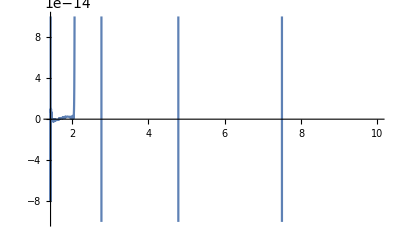

```mathematica
Plot[Re[hoo],{r,rp,10},PlotRange->10^-13]
```

```mathematica
Initψin[l_,m_,kin_,a_,M_,r0_] := 
Module[{i = l, j= m , N=kin, s = a, Μ=M, ρ0 = r0,f,k,ω,γ,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue},
rp= Μ+√(Μ^2-s^2);
rm = Μ-√(Μ^2-s^2);
ω = j/Μ(Μ/ρ0)^(3/2)/(1+(s/Μ)(Μ/ρ0)^(3/2));
γ = (2Μ rp ω-s j)/rp^2;
λ = Q[0,i,j,s ω];
f= {s^4 (2-3 k+k^2)-4 s j Μ rp^3 ω+s^2 rp (rp (2+12 k^2+j^2+k (-18-8 ⅈ rp γ)-λ+rp^2 ω^2)+Μ (-6+24 k-12 k^2+2 rp^2 ω^2))+rp^2 (4 (1-9 k+6 k^2) Μ^2+2 Μ rp (-1-20 k^2+2 k (12+5 ⅈ rp γ)+λ)-rp^2 (-15 k^2+3 k (5+4 ⅈ rp γ)+λ+rp^2 (γ^2-ω^2))),2 (-6 s j Μ rp^2 ω+s^2 (rp (13+4 k^2+j^2+6 ⅈ rp γ+k (-15-6 ⅈ rp γ)-λ+2 rp^2 ω^2)+Μ (-10+9 k-2 k^2+3 rp^2 ω^2))+rp ((26-30 k+8 k^2) Μ^2+Μ rp (-49-20 k^2-20 ⅈ rp γ+k (66+20 ⅈ rp γ)+3 λ)+rp^2 (20+10 k^2+15 ⅈ rp γ+k (-30-15 ⅈ rp γ)-2 λ-3 rp^2 (γ^2-ω^2)))),4 (-3+k)^2 Μ^2+2 Μ rp (-71-10 k^2-40 ⅈ rp γ+k (54+20 ⅈ rp γ)+3 λ)-12 s j Μ rp ω+s^2 (18+2 k^2+j^2+16 ⅈ rp γ+k (-12-8 ⅈ rp γ)-λ+6 Μ rp ω^2+6 rp^2 ω^2)+rp^2 (90+15 k^2+80 ⅈ rp γ+k (-75-40 ⅈ rp γ)-6 λ-15 rp^2 (γ^2-ω^2)),2 (-ⅈ s^2 (-3+k) γ-15 ⅈ (-3+k) rp^2 γ-10 rp^3 (γ^2-ω^2)+Μ (-28-2 k^2-30 ⅈ rp γ+5 k (3+2 ⅈ rp γ)+λ-2 s j ω+s^2 ω^2)+rp (36-21 k+3 k^2-2 λ+2 s^2 ω^2)),4+(-4+k)^2-k+4 ⅈ (-4+k) Μ γ-12 ⅈ (-4+k) rp γ-λ+s^2 ω^2-15 rp^2 (γ^2-ω^2),-2 ⅈ (-5+k) γ-6 rp γ^2+6 rp ω^2,-γ^2+ω^2};

cs = RecurrenceTable[{c[k] f⟦1⟧+c[-1+k] f⟦2⟧+c[-2+k] f⟦3⟧+c[-3+k] f⟦4⟧+c[-4+k] f⟦5⟧+c[-5+k] f⟦6⟧+c[-6+k] f⟦7⟧==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0,c[-5]==0},c,{k,0,N}]
]
ψin[l_,m_,kin_,a_,M_,r0_,r_,c_]:=Exp[-ⅈ ((2M(M+√(M^2-a^2))(m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2)))-a m)/((M+√(M^2-a^2))^2)) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n+1]](r-M-√(M^2-a^2))^n,{n,0,kin}]
```

```mathematica
ψin[2,2,100,.9,1,10,2,Initψin[2,2,100,.9,1,10]]
ψ[2]
```

-0.276649-2.19241 ⅈ

-0.276649-2.19241 ⅈ

```mathematica
cList= Initψin[2,2,100,.9,1,10];
```

General::munfl: 0.000011624^63 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000011624^64 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000011624^65 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

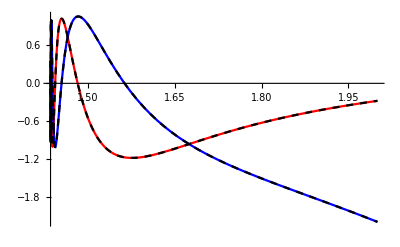

```mathematica
Show[
Plot[{Re[ψin[2,2,100,.9,1,10,r,cList]],Im[ψin[2,2,100,.9,1,10,r,cList ]]},{r,1+√(1-(.9)^2)+.0000001,2},PlotStyle->{Red,Blue}],

Plot[{Re[ψ[r]],Im[ψ[r]]},{r,1+√(1-(.9)^2)+.0000001,2},PlotStyle->{{Black,Dashed},{Black,Dashed}}]
]
```

```mathematica
cs==Initψin[2,2,100,.9,1,10]
```

True